### Reflection-Transmission profile

```mathematica
Reflection=FullSimplify[({{√(2γ1)}, {√(2γ2) Exp[ⅈ k x]}})ᵀ.Inverse[({{-ⅈ ω-ⅈ δ+2γ1+2γd, √(2γ1 2γ2) Exp[ⅈ k x]}, {√(2γ1 2γ2) Exp[ⅈ k x], -ⅈ ω-ⅈ δ+2γ2+2γd}})].({{-ⅈ √(2γ1)α}, {-ⅈ √(2γ2)α Exp[ⅈ k x]}})](*/.x->π/k*)/.{ω->0,α->1,γ1->1,γ2->1}
```

{{(2 (-2+4 ⅇ^(2 ⅈ k x)-2 γd-ⅇ^(2 ⅈ k x) (2+2 γd-ⅈ δ)+ⅈ δ))/(4 ⅈ ⅇ^(2 ⅈ k x)-ⅈ (2+2 γd-ⅈ δ)^2)}}

```mathematica
(**γ1,γ2 - decay rates of 1st and 2nd TLS to the waveguide, γd- "bad" decay, δ- detuning, kx - propagation phase, α- sqrt of the photon input rate (can be set α=1)**)
```

```mathematica
Transmission=FullSimplify[ⅈ α Exp[ⅈ k x]+({{√(2γ1)Exp[ⅈ k x]}, {√(2γ2)}})ᵀ.Inverse[({{-ⅈ ω-ⅈ δ+2γ1+2γd, √(2γ1 2γ2) Exp[ⅈ k x]}, {√(2γ1 2γ2) Exp[ⅈ k x], -ⅈ ω-ⅈ δ+2γ2+2γd}})].({{-ⅈ √(2γ1)α}, {-ⅈ √(2γ2)α Exp[ⅈ k x]}})]/.ω->0(*/.x->π/k*)(*/.{ω->0,α->1,δ->0,γ1->1,γ2->1}*)
```

{{(ⅇ^(ⅈ k x) α (4 (1+ⅇ^(2 ⅈ k x)) √γ1 √γ2 (-√γ1 √γ2+√(γ1 γ2))+(2 γd-ⅈ δ)^2))/(4 ⅈ ⅇ^(2 ⅈ k x) γ1 γ2-ⅈ (2 γ1+2 γd-ⅈ δ) (2 γ2+2 γd-ⅈ δ))}}

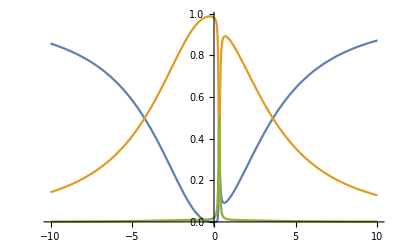

```mathematica
Block[{γ2=1,γ1=1,γd= 0.01,α=1,x=0.95 π/k},Plot[{Abs[Transmission/α^2]^2,Abs[Reflection/α^2]^2,1-Abs[Transmission/α^2]^2-Abs[Reflection/α^2]^2},{δ,-10,10},PlotRange->All]]
(*Transmission Reflection and Absorption*)
```

```mathematica
(**Propagation phase cannot be exactly n π because in this case dark state decouples from EM field. Small dip = dark state**)
```

### Electric field profile

```mathematica
(**driving by a point-like source**)
```

```mathematica
(*TOTAL field at position x1 with dipole located at x0*)
FIELD1=ⅈ α Exp[ⅈ k Abs[x1-x0]]+({{√(2γ1)Exp[ⅈ k Abs[x1]]}, {√(2γ2)Exp[ⅈ k Abs[x-x1]]}})ᵀ.Inverse[({{-ⅈ ω-ⅈ δ+2γ1+2γd, √(2γ1 2γ2) Exp[ⅈ k x]}, {√(2γ1 2γ2) Exp[ⅈ k x], -ⅈ ω-ⅈ δ+2γ2+2γd}})].({{-ⅈ √(2γ1)α Exp[ⅈ k Abs[x0]]}, {-ⅈ √(2γ2)α Exp[ⅈ k Abs[x-x0]]}})
```

{{ⅈ ⅇ^(ⅈ k Abs[-x0+x1]) α-ⅈ √2 ⅇ^(ⅈ k Abs[x-x0]) α √γ2 (-(2 √2 ⅇ^(ⅈ k x+ⅈ k Abs[x1]) √γ1 √(γ1 γ2))/(-4 ⅇ^(2 ⅈ k x) γ1 γ2+(2 γ1+2 γd-ⅈ δ-ⅈ ω) (2 γ2+2 γd-ⅈ δ-ⅈ ω))+(√2 ⅇ^(ⅈ k Abs[x-x1]) √γ2 (2 γ1+2 γd-ⅈ δ-ⅈ ω))/(-4 ⅇ^(2 ⅈ k x) γ1 γ2+(2 γ1+2 γd-ⅈ δ-ⅈ ω) (2 γ2+2 γd-ⅈ δ-ⅈ ω)))-ⅈ √2 ⅇ^(ⅈ k Abs[x0]) α √γ1 (-(2 √2 ⅇ^(ⅈ k x+ⅈ k Abs[x-x1]) √γ2 √(γ1 γ2))/(-4 ⅇ^(2 ⅈ k x) γ1 γ2+(2 γ1+2 γd-ⅈ δ-ⅈ ω) (2 γ2+2 γd-ⅈ δ-ⅈ ω))+(√2 ⅇ^(ⅈ k Abs[x1]) √γ1 (2 γ2+2 γd-ⅈ δ-ⅈ ω))/(-4 ⅇ^(2 ⅈ k x) γ1 γ2+(2 γ1+2 γd-ⅈ δ-ⅈ ω) (2 γ2+2 γd-ⅈ δ-ⅈ ω)))}}

```mathematica
(* The same but only the scattered part of the EM field*)
FIELD2=0ⅈ α Exp[ⅈ k Abs[x1-x0]]+({{√(2γ1)Exp[ⅈ k Abs[x1]]}, {√(2γ2)Exp[ⅈ k Abs[x-x1]]}})ᵀ.Inverse[({{-ⅈ ω-ⅈ δ+2γ1+2γd, √(2γ1 2γ2) Exp[ⅈ k x]}, {√(2γ1 2γ2) Exp[ⅈ k x], -ⅈ ω-ⅈ δ+2γ2+2γd}})].({{-ⅈ √(2γ1)α Exp[ⅈ k Abs[x0]]}, {-ⅈ √(2γ2)α Exp[ⅈ k Abs[x-x0]]}})
```

{{-ⅈ √2 ⅇ^(ⅈ k Abs[x-x0]) α √γ2 (-(2 √2 ⅇ^(ⅈ k x+ⅈ k Abs[x1]) √γ1 √(γ1 γ2))/(-4 ⅇ^(2 ⅈ k x) γ1 γ2+(2 γ1+2 γd-ⅈ δ-ⅈ ω) (2 γ2+2 γd-ⅈ δ-ⅈ ω))+(√2 ⅇ^(ⅈ k Abs[x-x1]) √γ2 (2 γ1+2 γd-ⅈ δ-ⅈ ω))/(-4 ⅇ^(2 ⅈ k x) γ1 γ2+(2 γ1+2 γd-ⅈ δ-ⅈ ω) (2 γ2+2 γd-ⅈ δ-ⅈ ω)))-ⅈ √2 ⅇ^(ⅈ k Abs[x0]) α √γ1 (-(2 √2 ⅇ^(ⅈ k x+ⅈ k Abs[x-x1]) √γ2 √(γ1 γ2))/(-4 ⅇ^(2 ⅈ k x) γ1 γ2+(2 γ1+2 γd-ⅈ δ-ⅈ ω) (2 γ2+2 γd-ⅈ δ-ⅈ ω))+(√2 ⅇ^(ⅈ k Abs[x1]) √γ1 (2 γ2+2 γd-ⅈ δ-ⅈ ω))/(-4 ⅇ^(2 ⅈ k x) γ1 γ2+(2 γ1+2 γd-ⅈ δ-ⅈ ω) (2 γ2+2 γd-ⅈ δ-ⅈ ω)))}}

```mathematica
plot=Show[Block[{γ2=1,γ1=1,γd= 0.01,α=1,x= 0.99 π/k,x0=0.5 x,δ=0,ω=0,k=1},Plot[{Abs[FIELD1]},{x1,-13,16},PlotRange->All,PlotStyle->Blue]],Block[{γ2=1,γ1=1,γd= 0.01,α=1,x= π/k,x0=0.5 x,δ=0,ω=0,k=1},Plot[{Abs[FIELD1]},{x1,-13,16},PlotRange->All,PlotStyle->Black]],Block[{γ2=1,γ1=1,γd= 0.01,α=1,x= 0.999 π/k,x0=0.5 x,δ=0,ω=0,k=1},Plot[{Abs[FIELD1]},{x1,-13,16},PlotRange->All,PlotStyle->{Red,Dashed}]],FrameLabel->{"x","E"},Frame->True];
```

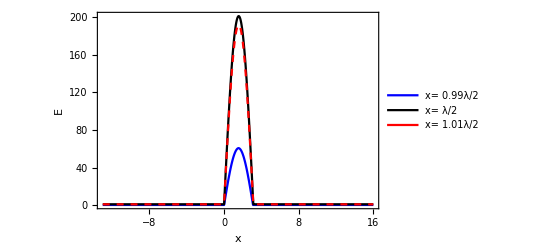

```mathematica
Legended[plot,LineLegend[{Blue,Black,Red},{"x= 0.99λ/2","x= λ/2","x= 1.01λ/2"}]]
```